## check the trap freq’s factor of √3??

```mathematica
PDF[Exp[-(x-x0)^2]]
```

PDF[ⅇ^(-(x-x0)^2)]

```mathematica
PDF[NormalDistribution[0,x]]
```

Exp[-1/2 ((#1-0)/x)^2]/(x √(2 π))&

```mathematica
Distribution
```

```mathematica
{Histogram3D[RandomVariate[BinormalDistribution[{1,2},{1.5,2},0.6],10^4],20,"PDF"],Plot3D[PDF[BinormalDistribution[{1,2},{1.5,2},0.6],{x,y}],{x,-5,6},{y,-3,7}]}
```

```mathematica
PDF[MaxwellDistribution[σ],x],{x,-Infinity, Infinity}
```

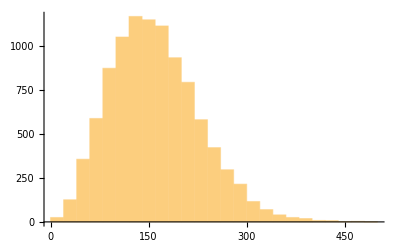

```mathematica
Tave=100;
data=RandomVariate[MaxwellDistribution[Tave],10^4];
Histogram[data]
```

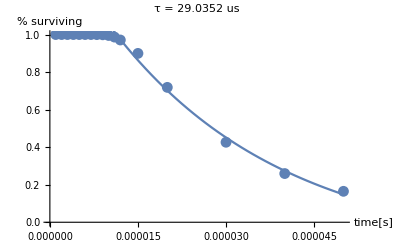

```mathematica
Clear["Global`*"]
nSim=10000;(*number of random atoms*)

T=2.5 10^-3; (*temp of atom in tweezer*)


Ttr=2.5 10^-3;

g=9.81;

kB = 1.38 10^-23;
mConv=1.66053892 10^-27;
m=132.9;
m=m mConv;

fax=30 10^3;
frad=120 10^3;
ωax=2π fax;
ωrad=2π frad;
Utr = kB Ttr;

Δxax=√((kB T)/(3 m ωax^2)); (*I don't know why I need the factor of √3 in these to get agreement*)
Δxrad=√((kB T)/(3 m ωrad^2));
Δv=√((kB T)/(3 m));

data=Reap[
Do[
xi1rad=RandomVariate[NormalDistribution[0,Δxrad],nSim];
xi2rad=RandomVariate[NormalDistribution[0,Δxrad],nSim];
xiax=RandomVariate[NormalDistribution[0,Δxax],nSim];

vi1rad=RandomVariate[NormalDistribution[0,Δv],nSim];
vi2rad=RandomVariate[NormalDistribution[0,Δv],nSim];
viax=RandomVariate[NormalDistribution[0,Δv],nSim];


xf1rad=vi1rad Δt;
xf2rad=vi2rad Δt-g Δt^2/2;
xfax=viax Δt;

Δx2=xf2rad-xi2rad; (*change in height*)

e=1/2 m(vi1rad^2+vi2rad^2+viax^2)+1/2 m(ωrad^2(xf1rad^2+xf2rad^2)+ωax^2 xfax^2)+m g Δx2;
surv=Less[#,Utr]&/@e;
survNum=Boole[surv];
Sow[{Δt,Total[survNum]/Length[survNum]}]
,{Δt,{1,2,3,4,5,6,7,8,9,10,11,12,15,20,30,40,50} 10^-6}(*rnr time*)
]
][[2,1]];
cutoff=10 10^-6; (*10*)
data2=Cases[data,x_/;x[[1]]>cutoff];
fitfn=A Exp[-t/τ]+Offs;

fit2=FindFit[data2, fitfn,{A,τ,Offs},t];
Show[{ListPlot[data,PlotRange->{All,{0,1}},PlotLabel->"τ = "<>ToString[10^6 τ/.fit2]<>" us",AxesLabel->{"time[s]","% surviving"}],
Plot[fitfn/.fit2,{t,0,50 10^-6}]}]
```